```mathematica
Clear["Global'*"]
eosG3crust=Import["/home/anto/ResearchProject2020/Anto/NuclearMatterEOS/core-crustEOS/crustMiyatsu/efpc_G3Crust.dat"]
```

(2.8226×10^-13 | 5.6044×10^-8
3.433×10^-13 | 6.2882×10^-8
4.1696×10^-13 | 7.0556×10^-8
5.0615×10^-13 | 7.9166×10^-8
6.141×10^-13 | 8.8826×10^-8
7.4466×10^-13 | 9.9663×10^-8
9.0245×10^-13 | 1.1182×10^-7
1.0931×10^-12 | 1.2547×10^-7
1.3233×10^-12 | 1.4078×10^-7
1.601×10^-12 | 1.5796×10^-7
1.9359×10^-12 | 1.7723×10^-7
2.3395×10^-12 | 1.9886×10^-7
2.8254×10^-12 | 2.2312×10^-7
3.4102×10^-12 | 2.5034×10^-7
4.1135×10^-12 | 2.8089×10^-7
4.9585×10^-12 | 3.1516×10^-7
5.9733×10^-12 | 3.5362×10^-7
7.1907×10^-12 | 3.9677×10^-7
8.6512×10^-12 | 4.4518×10^-7
1.04×10^-11 | 4.9951×10^-7
1.2494×10^-11 | 5.6046×10^-7
1.4999×10^-11 | 6.2882×10^-7
1.7993×10^-11 | 7.0556×10^-7
2.1568×10^-11 | 7.9166×10^-7
2.5834×10^-11 | 8.8826×10^-7
3.0921×10^-11 | 9.9669×10^-7
3.698×10^-11 | 1.1183×10^-6
4.4194×10^-11 | 1.2547×10^-6
5.2771×10^-11 | 1.4079×10^-6
6.2963×10^-11 | 1.5796×10^-6
7.5072×10^-11 | 1.7724×10^-6
8.9427×10^-11 | 1.9887×10^-6
1.0645×10^-10 | 2.2313×10^-6
1.2661×10^-10 | 2.5036×10^-6
1.5048×10^-10 | 2.8091×10^-6
1.787×10^-10 | 3.1519×10^-6
2.1206×10^-10 | 3.5365×10^-6
2.5145×10^-10 | 3.968×10^-6
2.9794×10^-10 | 4.4522×10^-6
3.5276×10^-10 | 4.9956×10^-6
4.1737×10^-10 | 5.6051×10^-6
4.9345×10^-10 | 6.2893×10^-6
5.83×10^-10 | 7.0567×10^-6
6.8837×10^-10 | 7.9178×10^-6
8.122×10^-10 | 8.8837×10^-6
9.5762×10^-10 | 9.968×10^-6
1.1285×10^-9 | 0.000011184
1.329×10^-9 | 0.00001255
1.5642×10^-9 | 0.000014081
1.84×10^-9 | 0.000015799
2.1632×10^-9 | 0.000017727
2.5418×10^-9 | 0.00001989
2.9852×10^-9 | 0.000022318
3.5042×10^-9 | 0.000025041
4.1114×10^-9 | 0.000028097
4.8216×10^-9 | 0.000031526
5.652×10^-9 | 0.000035373
6.6228×10^-9 | 0.00003969
7.7568×10^-9 | 0.000044534
9.0819×10^-9 | 0.000049969
1.0629×10^-8 | 0.000056068
1.2435×10^-8 | 0.00006291
1.4544×10^-8 | 0.00007059
1.7003×10^-8 | 0.000079206
1.9873×10^-8 | 0.000088871
2.3221×10^-8 | 0.000099714
2.7123×10^-8 | 0.00011189
3.1673×10^-8 | 0.00012554
3.6977×10^-8 | 0.00014086
4.3156×10^-8 | 0.00015806
5.0356×10^-8 | 0.00017735
5.8742×10^-8 | 0.000199
6.8506×10^-8 | 0.00022328
7.9878×10^-8 | 0.00025054
9.3122×10^-8 | 0.00028112
1.0853×10^-7 | 0.00031543
1.2646×10^-7 | 0.00035394
1.4733×10^-7 | 0.00039714
1.716×10^-7 | 0.00044562
1.9983×10^-7 | 0.00050001
2.3266×10^-7 | 0.00056106
2.7083×10^-7 | 0.00062955
3.152×10^-7 | 0.0007064
3.6678×10^-7 | 0.00079262
4.267×10^-7 | 0.00088938
4.9633×10^-7 | 0.00099798
5.7721×10^-7 | 0.0011198
6.7114×10^-7 | 0.0012565
7.8018×10^-7 | 0.0014099
9.0682×10^-7 | 0.001582
1.0538×10^-6 | 0.0017752
1.2243×10^-6 | 0.001992
1.4222×10^-6 | 0.0022352
1.6516×10^-6 | 0.0025081
1.9177×10^-6 | 0.0028144
2.2263×10^-6 | 0.003158
2.5839×10^-6 | 0.0035436
2.9983×10^-6 | 0.0039764
3.4783×10^-6 | 0.0044619
4.0343×10^-6 | 0.0050068
4.6781×10^-6 | 0.0056184
5.4233×10^-6 | 0.0063045
6.2857×10^-6 | 0.0070747
7.2831×10^-6 | 0.0079385
8.4365×10^-6 | 0.0089078
9.7703×10^-6 | 0.0099961
0.000011311 | 0.011217
0.000013092 | 0.012587
0.000015148 | 0.014125
0.000017522 | 0.01585
0.00002026 | 0.017787
0.00002342 | 0.01996
0.000027062 | 0.022398
0.000031258 | 0.025135
0.000036092 | 0.028206
0.000041657 | 0.031652
0.00004806 | 0.03552
0.000055423 | 0.03986
0.000063887 | 0.044731
0.000073605 | 0.050197
0.000084765 | 0.05633
0.00009756 | 0.063219
0.00011223 | 0.070943
0.00012903 | 0.079615
0.00014826 | 0.089348
0.00017024 | 0.10026
0.00019536 | 0.11252
0.00022402 | 0.12628
0.0002567 | 0.14172
0.00029391 | 0.15904
0.00033624 | 0.17849
0.00038432 | 0.20031
0.00043885 | 0.2248
0.00049218 | 0.25229
0.00053118 | 0.28313
0.00056027 | 0.31775
0.00059088 | 0.35659
0.00062508 | 0.40017
0.00066421 | 0.44908
0.00070409 | 0.50396
0.00074766 | 0.56555
0.00080227 | 0.63466
0.000865 | 0.71218
0.00093565 | 0.79918
0.0010167 | 0.89684
0.0011128 | 1.0064
0.0012254 | 1.1293
0.0013556 | 1.2673
0.001508 | 1.4221
0.0016855 | 1.5958
0.001892 | 1.7907
0.0021324 | 2.0095
0.0024125 | 2.255
0.0027382 | 2.5304
0.0031165 | 2.8395
0.0035557 | 3.1864
0.0040647 | 3.5756
0.0046542 | 4.0125
0.0053356 | 4.5027
0.0061226 | 5.0528
0.0070303 | 5.6701
0.0080758 | 6.3628
0.0092791 | 7.1403
0.010664 | 8.0126
0.012258 | 8.992
0.014095 | 10.091
0.016216 | 11.324
0.018677 | 12.708
0.021546 | 14.26
0.024921 | 16.004
0.028935 | 17.959
0.033777 | 20.155
0.039716 | 22.619
0.047138 | 25.383
0.056598 | 28.487
0.068893 | 31.971
0.085152 | 35.881
0.10698 | 40.271
0.13657 | 45.199
0.17691 | 50.733
0.23167 | 56.947
0.30567 | 63.931
0.39813 | 70.943
0.47796 | 75.7
0.5658 | 85.485
0.571382 | 85.8394
0.594092 | 87.2561
0.617571 | 88.6732
0.641841 | 90.0906
0.666923 | 91.5085
0.692838 | 92.9267)

-25739.3 P0^6+57536.1 P0^5-50531.6 P0^4+22272.3 P0^3-5263.62 P0^2+745.545 P0+0.0599175

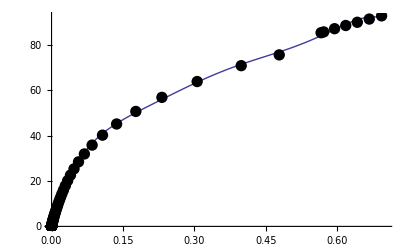

0.05991754822541613 + 745.5446229159369*P0 - 5263.623296380699*P0**2 + 22272.27407239779*P0**3 - 50531.61813700019*P0**4 + 57536.057965907225*P0**5 - 25739.27671913218*P0**6

```mathematica
FitG3Crust=Fit[eosG3crust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0]
FortranForm[FitG3Crust]
Plot[FitG3Crust,{P0,0,0.7},Epilog->{PointSize[0.02],Map[Point,eosG3crust]}]
```